```mathematica
SetDirectory[NotebookDirectory[]];
```

## Files and images

```mathematica
(* mma bitmap image makes files too large for github...*)
```

```mathematica
replaceJPG[head_] := Module[{res=head,img},
img=head["Image"];
jpgString = ExportString[ img,"JPG"];
res["ImageString"]=jpgString;
res=KeyDrop[res,{"Image"}];
res
];
```

```mathematica
(*head91=Import[FileNameJoin[PersistentSymbol["persistentGDrive"],"Work\\Textbook\\Springer\\SpringerMathematica\\Data\\head91HandCurated.mx"]];
head91=replaceJPG[head91];
Export[FileNameJoin[PersistentSymbol["persistentGitHubPath"],"MathematicalPhyllotaxis\\Mathematica\\Data","head91.mx"],head91];
head667=Import["E:\\Insync Gdrive\\Work\\Textbook\\Springer\\SpringerMathematica\\head667.mx"];
head667=replaceJPG[head667];
Export[FileNameJoin[PersistentSymbol["persistentGitHubPath"],"MathematicalPhyllotaxis\\Mathematica\\Data","head667.mx"],head667];

*)
loadHead[headID_] := Module[{file,head},
file = FileNameJoin[PersistentSymbol["persistentGitHubPath"],"MathematicalPhyllotaxis\\Mathematica\\Data",
StringJoin["head",ToString[headID],".mx"]];
head= Import[file];
If[!KeyMemberQ[head,"Image"] && KeyMemberQ[head,"ImageString"],
head["Image"]=ImportString[head["ImageString"],"JPG"];
head=KeyDrop[head,{"ImageString"}]
];
head
];
saveHead[head_] := Module[{headID,headJPG},
headID=head["ID"];
headJPG=replaceJPG[head];
Export[FileNameJoin[PersistentSymbol["persistentGitHubPath"],"MathematicalPhyllotaxis\\Mathematica\\Data",StringJoin["head",ToString[headID],".mx"]],headJPG];

]
```

```mathematica
(*addMesh[head_]:= Module[{lineNodes,m} ,
lineNodes=Map[#["ThreadNodes"]&,head["Threads"]]; (* may not be right *)
m=MeshRegion[Values@head["Seeds"],Map[Line,lineNodes]];
Append[head,"Mesh"->m]
];
*)
```

## Initial seed placements

```mathematica
(* legacy code would need to be refactored *)
```

```mathematica
deleteLastPointFromThread[threadAssociation_] := Module[{res,currentThreadKey},
res=threadAssociation;
currentThreadKey=Last@Keys@threadAssociation;
If[Length[res[currentThreadKey]]>0,
res[currentThreadKey]=Drop[res[currentThreadKey],-1]];
res 
];
```

```mathematica
capturePoint[]:= Round/@MousePosition["Graphics"];
```

```mathematica
newThread[threadAssociation_] := Module[{threadID},
threadID=If[Length[threadAssociation]==0,1,Max[Keys[threadAssociation]]+1];
Append[threadAssociation,threadID->{}]
];
```

```mathematica
scol[threadAssociation_] := Module[{lastThread,lastPoint},
If[Length[threadAssociation]==0,lastThread={},lastThread=Last[threadAssociation]];
If[Length[lastThread]==0,lastPoint={},lastPoint=Last[lastThread]];
Show[Image[i667,ImageSize->Large],
Graphics[
{Map[{Green,Line[#]}&,Values[threadAssociation]],
{Yellow,Point[lastThread]},
{Red,Point[lastPoint]}
}
]]
];
addPointToThread[threadAssociation_,point_] := Module[{res,currentThreadKey},
res=threadAssociation;
currentThreadKey=Last@Keys@threadAssociation;
res[currentThreadKey]=Append[res[currentThreadKey],point];
res 
];
```

```mathematica
pointCollector[threadsKnown_:<|1->{}|>] := Module[{},
DynamicModule[{point=Missing[],threadAssociation=threadsKnown},
Column@{
Row[{
Button["Undo point",threadAssociation=deleteLastPointFromThread[threadAssociation]],
Button["Make thread",threadAssociation=newThread[threadAssociation]],
Button["Print thread",Print[threadAssociation]]
}],
Dynamic[globalThreads=threadAssociation;
Length/@threadAssociation],
EventHandler[
Dynamic[
scol[threadAssociation] ],
"MouseDown":>(
point= Round/@MousePosition["Graphics"];
threadAssociation=addPointToThread[threadAssociation,point];
)]
}]
];
```

```mathematica
(*
pointCollector[]
*)
```

```mathematica
(* format of the threads data continues to evolve *)
```

```mathematica
(*
enumerate[list_] := Association@Thread[Range[Length[list]]->list];makePointsFromThreads[threadAssociation_] := enumerate[Join@@Values@threadAssociation];
seeds = makePointsFromThreads [globalThreads];
seedLookup=Association@Thread[Values[seeds]->Keys[seeds]];
threads= Map[seedLookup,globalThreads,{2}];
threads=KeyValueMap[<|"Family"->1,"ThreadID"->#1,"ThreadNodes"->#2|>&,threads];
*)
```

```mathematica
fom[x_]:=If[Length[x]>0,First[x],Missing[x]];
```

```mathematica
(*pointPicker[head667]*)
```

## Make graph from seed positions

```mathematica
(* check we didnt muck up the mesh*)
```

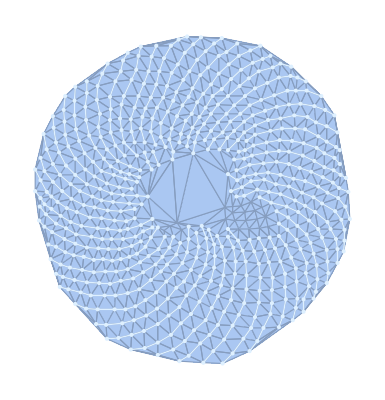

```mathematica
(*nodes=Values@head667["Seeds"];
mesh = DelaunayMesh[nodes];
Show[mesh,graphicsHeadLines[head667,1]]
head667["Mesh"]=mesh;
head667["Graph"]=graphFromMesh[mesh];
head667["Graph"]=addBoundaryCoordinatesToGraph[head667["Graph"]];
head667=addThreadEdges[head667];
saveHead[head667]
*)
```

```mathematica
graphFromMesh[mesh_]:=Module[{g,pts,edges,ptXY},
g=MeshConnectivityGraph[mesh,0];pts=Last/@VertexList[g];edges=Map[Last,EdgeList[g],{2}];ptXY=(#1->AnnotationValue[{g,{0,#1}},VertexCoordinates]&)/@pts;g=Graph[(Tooltip[#1,#1]&)/@pts,edges,VertexCoordinates->ptXY];
g
]
```

#### Boundary finding

```mathematica
boundaryGraph[graph_] := Module[{leftMostNode,leftMostEdge,res,pathAsEdges},
leftMostNode = First@SortBy[VertexList[graph],AnnotationValue[{graph,#},VertexCoordinates][[1]]&];
leftMostEdge = fom@SortBy[centredVertexList[graph,leftMostNode],edgeClockTime[graph,#]&];
If[MissingQ[leftMostEdge],Return[Missing["No edges left"]]];
pathAsEdges=Catch[Nest[nextPath[graph,#]&,{leftMostEdge},1000]];
pathAsEdges=orderUndirectedEdges[pathAsEdges];
res=subGraphEdgesOnly[graph,pathAsEdges];
res=Graph[res,EdgeShapeFunction->{"Arrow"}];
res
];
centredVertexList[graph_,v_] := Module[{unsortedEdgeList,otherVertices},
unsortedEdgeList= EdgeList[graph,v<->_];
otherVertices=Complement[Flatten[List@@@unsortedEdgeList],{v}];
Map[v<->#&,otherVertices]
];
edgeClockTime[graph_,edge_] := Module[{v1,v2},
{v1,v2}=N@Map[AnnotationValue[{graph,#},VertexCoordinates]&,List@@edge];
12*Mod[π/2-ArcTan@@(v2-v1),2π]/(2π)
];
edgeClockTime[graph_,edge1_,edge2_] := Module[{t1,t2},
t1=edgeClockTime[graph,edge1];
t2=edgeClockTime[graph,edge2];
Mod[t2-t1-6,12] (* so time[ a<->b, b<->a] =0*)
];
edgeDeviation[graph_,edge1_,edge2_] := Module[{edgeTime},
edgeTime=edgeClockTime[graph,edge1,edge2];
Abs[edgeTime-6] 
];
nextPath[graph_,path_] := Module[{n},
n=nextEdgeByClockTime[graph,Last[path]];
If[MissingQ[n],(*Print["No nxt node"];*)Throw[path]];
If[MemberQ[path,n],Throw[path]];
Append[path,n]
];
nextEdgeByClockTime[graph_,v1_<->v2_] :=Module[{es,nextv},
es=nextEdgesByClockTime[graph,v1<->v2];
es=KeyDrop[es,v2 <-> v1] ;(* reverse edge*)
fom[Keys[es]]
];
nextEdgesByClockTime[graph_,v1_<->v2_] := Sort@Association@
Map[#->edgeClockTime[graph,v1<->v2,#]&,
centredVertexList[graph,v2]];

orderUndirectedEdges[chain_] := Module[{lastb,examinePair},
lastb=chain[[1,1]];
examinePair[a_<->b_] := Module[{res},
res= If[a=!=lastb,b->a,a->b];
lastb=b;
res
];
Map[examinePair,chain]
];
subGraphEdgesOnly[graph_,sg_Graph]:=  subGraphEdgesOnly[graph,EdgeList[sg]];
subGraphEdgesOnly[graph_,edges_] := Module[{g,e},
g=EdgeDelete[graph,EdgeList[graph]];
g= EdgeAdd[g,edges];
g=Subgraph[g,edges];
g
];
stripBoundary[<|"Graph"->graph_,___,"Level"->level_,___|>] := Module[{bge,remainder,bv,bg},
bge=boundaryGraphEdges[graph];
If[MissingQ[bge],Return[bge]];
bv= VertexList[Graph[bge]];
remainder=Subgraph[graph,Complement[VertexList[graph],bv]];
bg= subGraphEdgesOnly[graph,bge];
<|"Graph"->remainder,"Level"->level+1,"Boundary"->bg,"BoundaryDirectedEdges"->bge|>
];
boundaryGraphEdges[graph_] := Module[{g,e},
g=boundaryGraph[graph];
If[MissingQ[g],Return[g]];
e=FindCycle[g];
fom@e
];
nodeBoundaryCoordinatesLookupLevel[graphBoundaryList_,level_] := Module[{g,v,np},
g=graphBoundaryList[[level]];
v=VertexList[g];
np=Length[v];
Association@Table[v[[nodeix]]-><|"Node"->v[[nodeix]],"Level"->level,"Y"->nodeix,"adjacentY"->{If[nodeix==1,np,nodeix-1],If[nodeix==np,1,nodeix+1]}
|>,{nodeix,np}]
];
makeNodeBoundaryCoordinatesLookup[graphBoundaryList_]:=
Join@@Map[nodeBoundaryCoordinatesLookupLevel[graphBoundaryList,#]&,Range[Length[graphBoundaryList]]];

makeBoundaryCoordinates[graph_] := Module[{stripResults,boundaryCoordinateLength,graphBoundaryList,boundaryCoordinatesLookup},
stripResults=DeleteMissing@NestWhileList[stripBoundary,<|"Graph"->graph,"Boundary"->_,"Level"->0|>,!MissingQ[#]&,1,20];
graphBoundaryList =Drop[#Boundary&/@stripResults,1];
boundaryCoordinatesLookup =makeNodeBoundaryCoordinatesLookup[graphBoundaryList];
boundaryCoordinatesLookup
];

addBoundaryCoordinatesToGraph[graphArg_] := Module[{graph=graphArg,bc},
bc=makeBoundaryCoordinates[graph];
Map[(AnnotationValue[{graph,#},"BoundaryCoordinates"]=bc[#])&,VertexList[graph]];
graph
]
```

### Thread finding

```mathematica
nodeOrdering[graph_,a_,b_]:= Module[{bc},
bc[node_] := AnnotationValue[{graph,node},"BoundaryCoordinates"];
If[MissingQ[bc[a]]|| MissingQ[bc[a]["Level"]],Return[False]];
If[MissingQ[bc[b]]|| MissingQ[bc[b]["Level"]],Return[True]];
If[bc[a]["Level"]<  bc[b]["Level"],Return[True]];
If[bc[b]["Y"]==1 && bc[a]["Y"]==bc[b]["adjacentY"][[1]],Return[True]];
Return[bc[a]["Y"]< bc[b]["Y"]];
];


sortEdge[graph_,a_<->b_] := Module[{pair},
pair={a,b};
pair = Sort[pair,nodeOrdering[graph,#1,#2]&];
UndirectedEdge@@pair
];

makeSortedThreadEdges[graph_,thread_] := Module[{g,edges},
g=Subgraph[graph,thread["ThreadNodes"]];
edges = EdgeList[g];
If[nodeOrdering[graph,edges[[1,1]],edges[[-1,-1]]],
edges,Reverse/@(Reverse[edges])]
];

addThreadEdges[head_]:= Module[{res=head,threads},
threads=head["Threads"];
threads=Map[Append[#,"ThreadEdges"->makeSortedThreadEdges[head["Graph"],#]]&,threads];
res["Threads"]=threads;
res 
];
```

```mathematica
threadsSeededAt[graph_,a_] := Module[{edgePairs},
edgePairs=edgeMatch[graph,a];
threads=Association@Map[#->extendThreadFromSeed[graph,#]&,edgePairs]
];

extendThreadFromSeed[graph_,seed_] :=Module[{thread},
thread = Catch[Nest[findNextEdgeInThread[graph,#,"Inwards"]&,seed,100]];
thread = Catch[Nest[findNextEdgeInThread[graph,#,"Outwards"]&,thread,100]];
thread 
];

findNextEdgeInThread[graph_,thread_,direction_] := Module[{lastEdge,lastNode,nextNodes,bottomLevel,level},
bottomLevel = Max@Map[#Level&,DeleteMissing[AnnotationValue[{graph,#},"BoundaryCoordinates"]]&/@VertexList[graph]];
lastEdge=If[direction=="Inwards",Last[thread],First[thread]];
lastNode=If[direction=="Inwards",Last[lastEdge],First[lastEdge]];
nextNodes= AdjacencyList[graph,lastNode];
res=Map[ <|"LastNode"->lastNode,"NextNode"->#,"NextEdge"-> If [direction=="Inwards",lastNode <-> #,#<->lastNode]|>&,nextNodes];
res= Map[Append[#,"Deviation"->edgeDeviation[graph,lastEdge,#NextEdge]]&,res];
res = Select[res,#Deviation<1&];
res = fom@res;
If[MissingQ[res],Throw[thread]];
nextNode= fom@Complement[List@@res["NextEdge"],{lastNode}];
level = AnnotationValue[{graph,nextNode},"BoundaryCoordinates"];
If[MissingQ[level],Throw[thread]];
If[level["Level"]==1,Throw[thread]];
If[level["Level"]==bottomLevel,Throw[thread]];
res = If[direction=="Inwards",
Append[thread,res["NextEdge"]]
,
Prepend[thread,res["NextEdge"]]
];
res
];

(* pairs of edges which can form threads *)
edgeMatch[graph_,node_] := Module[{ng,edges,refNode,level,nbrs,nodeTimes,edgePairs,bc},
edges=EdgeList[graph,_<->node];
nbrs=Complement[VertexList[Graph[edges]],{node}];
bc= Association@Map[#-> AnnotationValue[{graph,#},"BoundaryCoordinates"]&,nbrs];
If[EvenQ[Length[nbrs]],
level=bc[node]["Level"];
refNode=First[nbrs];
nodeTimes =Association@Map[node <-># -> edgeClockTime[graph,refNode <-> node,node <->#]&,nbrs];
nodeTimes=Sort[nodeTimes];
edgePairs= Transpose[Partition[Keys[nodeTimes],Length[nbrs]/2]];
edgePairs = Map[sortEdgeListByLevel[graph,#]&,edgePairs]
(* by construction, these pairs all radiate from the node *)
,
(* odd # of edges *)
(*Print["Nonhex ", node, " ",Length[nbrs]];
*)edgePairs=edgeMatchByDeviation[graph,node]
];
edgePairs
];
edgeMatchByDeviation[graph_,node_]:= 
Module[{ng,edges,nbrs,edgePairs,maxPairs,leftOver,bc,edgePairDeviations},
bc[n_]:=  AnnotationValue[{graph,n},"BoundaryCoordinates"];
edges=EdgeList[graph,_<->node];
nbrs=Complement[VertexList[Graph[edges]],{node}];
maxPairs=Floor[Length[nbrs]/2];
edgePairs= Subsets[edges,{2}];
edgePairDeviations = Association@Map[#->edgeDeviation[graph,#[[1]],#[[2]] ]&,edgePairs];
edgePairDeviations= Sort[edgePairDeviations];
edgePairs=Keys[edgePairDeviations];
edgePairs= removeDuplicateEdges[edgePairs];
edgePairs= Take[edgePairs,UpTo[maxPairs]];
If[edgePairDeviations[Last[edgePairs]]>2,Print["Large deviation ",edgePairs]];
If[OddQ[Length[nbrs]],
leftOver= List/@Complement[edges,Flatten[edgePairs]];
edgePairs=Join[edgePairs,leftOver]
];
edgePairs
];
removeDuplicateEdges [edgePairList_] := Module[{used,i,nextPair},
used = {};nextPair={};
For[i=1,i<=Length[edgePairList],i++,
nextPair= Append[nextPair,Complement[edgePairList[[i]],used]];
used=Join[used,edgePairList[[i]]];
];
Select[nextPair,Length[#]==2&]
];
sortEdgeListByLevel[graph_,{node_<->a_,node_ <->b_}] := Module[{bc},
bc[n_]:=  AnnotationValue[{graph,n},"BoundaryCoordinates"];
(
If[(bc[a]["Level"]< bc[b]["Level"] )||((bc[a]["Level"]== bc[b]["Level"]) && bc[a]["Y"]< bc[b]["Y"]),{a<->node,node <->b},{b<->node,node <->a }])
];
```

## Thread mangling

```mathematica
displayHead[head_,currentFamily_,nearestNode_,currentThread_] := Module[{nodesInThreads,threadList,lineNodes,linesXY,threadLines,node},
threadList=head["Threads"];
lineNodes=Association@Map[#ThreadID->#["ThreadNodes"]&,threadList];
nodesInThreads=Map[head["Seeds"],lineNodes,{2}];
linesXY=Map[Line,nodesInThreads];
pointsXY=Map[Point,nodesInThreads];
If[MissingQ[nearestNode],node={},
node={Red,PointSize[Large],Point[head["Seeds"][nearestNode]]}];
If[MissingQ[currentThread],threadLines={},threadLines={Red,linesXY[currentThread]}];
Show[
displayHeadFamily[head,currentFamily,300],
Graphics[
{
node
,threadLines
}]
]
];

displayHeadFamilies[head_] := Row[Map[displayHeadFamily[head,#]&,familiesOfHead[head]]];
displayHeadFamily[head_,familyID_,imageSize_:150] := 
Module[{nodesInThreads,threadList,lineNodes,linesXY,pointsXY},
threadList=Select[head["Threads"],#Family==familyID&];
lineNodes=Association@Map[#ThreadID->#["ThreadNodes"]&,threadList];
nodesInThreads=Map[head["Seeds"],lineNodes,{2}];
linesXY=Map[Line,nodesInThreads];
pointsXY=Map[Point,nodesInThreads];
Show[
Image[head["Image"],ImageSize->imageSize],
Graphics[
{
{LightBlue,Values[linesXY],Values[pointsXY]},
}]
]
];

graphicsHeadLines[head_,familyID_,imageSize_:150] := 
Module[{nodesInThreads,threadList,lineNodes,linesXY,pointsXY},
threadList=Select[head["Threads"],#Family==familyID&];
lineNodes=Association@Map[#ThreadID->#["ThreadNodes"]&,threadList];
nodesInThreads=Map[head["Seeds"],lineNodes,{2}];
linesXY=Map[Line,nodesInThreads];
pointsXY=Map[Point,nodesInThreads];
Graphics[
{
{LightBlue,Values[linesXY],Values[pointsXY]}
}]
];

threadsThroughNode[graph_,selectedNode_,nextNode_] := Module[{threadPossibles},
If[MissingQ[selectedNode],Return[{}]];
threadPossibles = threadsSeededAt[graph,selectedNode];
If[MissingQ[nextNode],Return[threadPossibles]];
threadPossibles=Select[threadPossibles,MemberQ[VertexList[#],nextNode]&];
threadPossibles
];


displayHeadThreads[head_,currentFamily_,selectedNode_]:= displayHeadThreads[head,currentFamily,Missing[],selectedNode];
displayHeadThreads[head_,currentFamily_,nextNode_,selectedNode_] := Module[{threadPossibles,threadPossibleEdges,g},
g = EdgeDelete[head["Graph"],Flatten[#ThreadEdges&/@head["Threads"]]];
threadPossibleEdges=Flatten@Values@threadsThroughNode[g,selectedNode,nextNode];
Show[
Graphics[Rectangle[{0,0},ImageDimensions[head["Image"]]],ImageSize->300],
Image[head["Image"],ImageSize->300],
HighlightGraph[Graph[g,BaseStyle->White],threadPossibleEdges]
]
];
```

## Thread moving

```mathematica
addFamily[head_] := Module[{res=head},res["FamilyCount"]=res["FamilyCount"]+1;res];
familiesOfHead[head_]:=Range[head["FamilyCount"]];
nextFamilyID[head_,familyID_] := If[familyID>=head["FamilyCount"],1,familyID+1];

threadsByFamily[head_]:= GroupBy[head["Threads"],#Family&];
expandThread[thread_] := Map[Append[KeyDrop[thread,{"ThreadNodes"}],"Node"->#]&,thread["ThreadNodes"]]

moveThreadToNextFamily[head_,currentThreadID_] := Module[{res,currentThreadPosition,threads,thread,familyID},
threads=head["Threads"];
currentThreadPosition=fom@fom@Position[threads,<|___,"ThreadID"->currentThreadID,___|>];
thread=head["Threads"][[currentThreadPosition]];
familyID=thread["Family"];
familyID=nextFamilyID[head,familyID];
thread["Family"]=familyID;
threads[[currentThreadPosition]]=thread;
res=head;
res["Threads"]=threads;
res
];

threadEdgesThroughNodePair[head_,lastNode_,nearestNode_] := fom@Values@threadsThroughNode[head["Graph"],lastNode,nearestNode];

addThreadToFamily[headArg_,currentFamily_,threadEdges_] := Module[{head=headArg,,threadNodes,familyThreads,threadID},
threadNodes = VertexList[threadEdges];
familyThreads = Select[head["Threads"],#Family==currentFamily&];
threadID = If[Length[familyThreads]==0,1,Max[#ThreadID&/@familyThreads]+1];
head["Threads"]=Append[head["Threads"],
<|"Family"->currentFamily,"ThreadID"->threadID,"ThreadNodes"->threadNodes,"ThreadEdges"->threadEdges|>];
head
];
```

```mathematica
threadMover[headArg_] := DynamicModule[{
currentFamily=1,
currentThreadID=Missing[],
mode="ThreadSelect",
nearestNode=Missing[],
nodeLookup,
point,familyCount,
head=headArg},
nodeLookup[head_]:= First/@GroupBy[Flatten@Map[expandThread,head["Threads"]],(#Node&)];
familyCount=3;
Column@{
(*SetterBar[Dynamic[mode],{"ThreadSelect"->"Thread select"}],*)mode="ThreadSelect";
Button["Add family",
familyCount++;head["FamilyCount"]=familyCount],
Button["Move thread to next family",
head=moveThreadToNextFamily[head,currentThreadID]],
Button["Save",
saveHead[head]
],
Dynamic@SetterBar[Dynamic[currentFamily],Range[familyCount]],
(*Dynamic[StringJoin["Current thread ",ToString[Select[head["Threads"],#ThreadID==currentThreadID&]]]],
Dynamic[StringJoin["Threads by family ",ToString[Length/@threadsByFamily[head]]]],
*)

EventHandler[
Dynamic[
displayHead[head,currentFamily,nearestNode,currentThreadID] ],
"MouseDown":>(
point= MousePosition["Graphics"];
nearestNode=Last@Last@NearestMeshCells[{head["Mesh"],0},point];
(*If[mode=="ThreadSelect",
currentThreadID=nodeLookup[head][nearestNode]["ThreadID"]];
If[mode!="ThreadSelect",
currentThreadID=Missing[]];*)
currentThreadID=nodeLookup[head][nearestNode]["ThreadID"];
)],
Dynamic[displayHeadFamilies[head]]
}];
```

```mathematica
head667=loadHead[667];
threadMover[head667]
```

## Thread creation

```mathematica
threadCreator[headArg_] := DynamicModule[{
currentFamily=3,
mode="NodeSelect",
lastNode=Missing[],
nearestNode=Missing[],
nodeLookup,
point,familyCount,
pruneTailNodes=0,
head=headArg},
nodeLookup[head_]:= First/@GroupBy[Flatten@Map[expandThread,head["Threads"]],(#Node&)];
familyCount=3;
Column@{
SetterBar[Dynamic[mode],{"NodeSelect"->"Node select","ThreadSelect"->"Thread select"}],
Row[{"Prune tail nodes ", Dynamic[pruneTail],Slider[Dynamic[pruneTail],{0,10,1}]}], 
Button["Save",
saveHead[head]
],
Button["Add to family",
head=addThreadToFamily[head,currentFamily,threadEdgesThroughNodePair[head,lastNode,nearestNode] ]
],
Row[{"Current family",Dynamic@SetterBar[Dynamic[currentFamily],Range[familyCount]]}],
Dynamic[{lastNode,nearestNode}],
EventHandler[
Dynamic[
Switch[mode,
"NodeSelect",displayHeadThreads[head,currentFamily,nearestNode]
,
"ThreadSelect",displayHeadThreads[head,currentFamily,lastNode,nearestNode]
 ]],
"MouseDown":>(
point= MousePosition["Graphics"];
lastNode=nearestNode;
nearestNode=Last@Last@NearestMeshCells[{head["Mesh"],0},point];
If[mode=="NodeSelect",mode="ThreadSelect"];
)],
Dynamic[displayHeadFamilies[head]],
Button["Add family",
familyCount++;head["FamilyCount"]=familyCount]
}];
```

```mathematica
head667=loadHead[667];
threadCreator[head667]
```